```mathematica
f(x) = 2x
```

Set::write: Tag Times in f\ x is Protected.

2 x

```mathematica
f[x] = 2x
```

2 x

```mathematica
f[3]
```

f[3]

```mathematica
f[x_] := 2x
```

```mathematica
f[2]
```

4

```mathematica
f[x_]:=1/(1 + x^2)
```

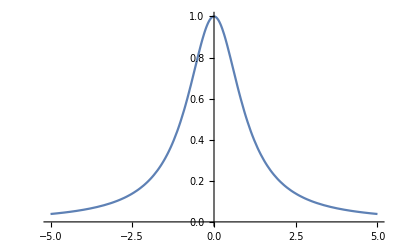

```mathematica
Plot[f[x], {x, -5, 5}]
```

```mathematica
A = {{1, 1, 1, 1}, {0, 1/3, 1/2, 1}, {0, 18, 1/8, 1/2}, {0, 1/81, 1/16, 1}}
```

{{1,1,1,1},{0,1/3,1/2,1},{0,18,1/8,1/2},{0,1/81,1/16,1}}

```mathematica
LinearSolve[A, {{0}, {1}, {0}, {0}}]
```

{{-43485/20327},{-243/20327},{46640/20327},{-2912/20327}}

```mathematica
N[MatrixForm[{{-43485/20327},{-243/20327},{46640/20327},{-2912/20327}}]]
```

(-2.13927
-0.0119545
2.29449
-0.143258)

```mathematica
InterpolatingPolynomial[{{1, 1}, {2, 2}, {4, 3}, {8, 4}}, x]
```

1+(1+(-1/6+1/56 (-4+x)) (-2+x)) (-1+x)

```mathematica
Expand[1+(1+(-1/6+1/56 (-4+x)) (-2+x)) (-1+x)]
```

-10/21+(7 x)/4-(7 x^2)/24+x^3/56

```mathematica
B = {{1, 1, 1, 1}, {1, 2, 4, 8}, {1, 4, 16, 64}, {1, 8, 64, 8^3}}
```

{{1,1,1,1},{1,2,4,8},{1,4,16,64},{1,8,64,512}}

```mathematica
LinearSolve[B, {{1}, {2}, {3}, {4}}]
```

{{-10/21},{7/4},{-7/24},{1/56}}

```mathematica
InterpolatingPolynomial[{5.0,0.0,-1.6666666666666665,-2.5,-3.0,-3.333333333333333,-3.571428571428571,-3.75,-3.888888888888889,-4.0,-4.090909090909091,-4.166666666666667,-4.230769230769231,-4.285714285714286,-4.333333333333333,-4.375,-4.411764705882353,-4.444444444444445,-4.473684210526316,-4.5}, x]
```

-4.5+(-0.5+(0.05+(-0.003125+(0.00078125+(-0.0000434028+(6.2004×10^-6+(-3.1002×10^-6+(2.38477×10^-7+(-1.25514×10^-8+(4.1838×10^-9+(-2.98843×10^-10+(4.98072×10^-11+(-2.92983×10^-12+(3.25537×10^-13+(-6.51074×10^-14+(5.42562×10^-15+(-3.61708×10^-16+(4.52135×10^-17-4.11032×10^-18 (-8+x)) (-15+x)) (-12+x)) (-5+x)) (-9+x)) (-17+x)) (-6+x)) (-14+x)) (-3+x)) (-19+x)) (-13+x)) (-2+x)) (-7+x)) (-18+x)) (-4+x)) (-16+x)) (-10+x)) (-1+x)) (-20+x)

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
Plot[y[x], {x, -5, 5}]
```

-Graphics-

```mathematica
f[x_]:=1/(1 + x^2)
```

```mathematica
points = {{-5, f[-5]}, {-4.5, f[-4.5]}, {-4, f[-4]}, {-3.5, f[-3.5]}, {-3, f[-3]}, {-2.5, f[-2.5]}, {-2, f[-2]}, {-1.5, f[-1.5]}, {-1, f[-1]}, {-.5, f[-.5]}, {0, f[0]}, {.5, f[.5]}, {1, f[1]}, {1.5, f[1.5]}, {2, f[2]}, {2.5, f[2.5]}, {3, f[3.5]}, {3.5, f[3.5]}, {4, f[4]}, {4.5, f[4.5]}, {5, f[5]}}
```

{{-5,1/26},{-4.5,0.0470588},{-4,1/17},{-3.5,0.0754717},{-3,1/10},{-2.5,0.137931},{-2,1/5},{-1.5,0.307692},{-1,1/2},{-0.5,0.8},{0,1},{0.5,0.8},{1,1/2},{1.5,0.307692},{2,1/5},{2.5,0.137931},{3,0.0754717},{3.5,0.0754717},{4,1/17},{4.5,0.0470588},{5,1/26}}

```mathematica
fx = InterpolatingFunction[points]
```

InterpolatingFunction[{{-5,1/26},{-4.5,0.0470588},{-4,1/17},{-3.5,0.0754717},{-3,1/10},{-2.5,0.137931},{-2,1/5},{-1.5,0.307692},{-1,1/2},{-0.5,0.8},{0,1},{0.5,0.8},{1,1/2},{1.5,0.307692},{2,1/5},{2.5,0.137931},{3,0.0754717},{3.5,0.0754717},{4,1/17},{4.5,0.0470588},{5,1/26}}]

```mathematica
Plot[fx[x], {x, -5, 5}]
```

-Graphics-

```mathematica
PlotRange[points]
```

PlotRange::gtype: List is not a type of graphics.

PlotRange[{{-5,1/26},{-4.5,0.0470588},{-4,1/17},{-3.5,0.0754717},{-3,1/10},{-2.5,0.137931},{-2,1/5},{-1.5,0.307692},{-1,1/2},{-0.5,0.8},{0,1},{0.5,0.8},{1,1/2},{1.5,0.307692},{2,1/5},{2.5,0.137931},{3,0.0754717},{3.5,0.0754717},{4,1/17},{4.5,0.0470588},{5,1/26}}]

```mathematica
fx[1]
```

```mathematica
InterpolatingFunction[{{-5,1/26},{-4.5,0.047058823529411764},{-4,1/17},{-3.5,0.07547169811320754},{-3,1/10},{-2.5,0.13793103448275862},{-2,1/5},{-1.5,0.3076923076923077},{-1,1/2},{-0.5,0.8},{0,1},{0.5,0.8},{1,1/2},{1.5,0.3076923076923077},{2,1/5},{2.5,0.13793103448275862},{3,0.07547169811320754},{3.5,0.07547169811320754},{4,1/17},{4.5,0.047058823529411764},{5,1/26}}][1]
```

InterpolatingFunction::noinfo: Input expression InterpolatingFunction[{{-5, 1/26}, {-4.5`, 0.047058823529411764`}, {-4, 1/17}, {-3.5`, 0.07547169811320754`}, {-3, 1/10}, {-2.5`, 0.13793103448275862`}, {-2, 1/5}, {-1.5`, 0.3076923076923077`}, « 6 », {2, 1/5}, {2.5`, 0.13793103448275862`}, {3, 0.07547169811320754`}, {3.5`, 0.07547169811320754`}, {4, 1/17}, {4.5`, 0.047058823529411764`}, {5, 1/26}}] contains insufficient information to interpret the result.

```mathematica
fx = Interpolation[points, Method -> "Piecewise"]
```

InterpolatingFunction[{{-5., 5.}}, <>]

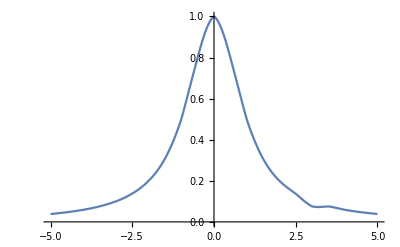

```mathematica
Plot[fx[x], {x, -5, 5}]
```

```mathematica
f
```

f

```mathematica
f[x]
```

2 x

```mathematica
f[1]
```

1/2

```mathematica
f[2]
```

1/5

```mathematica
p[x_]:=InterpolatingPolynomial[points, x]
```

```mathematica
Function[x,InterpolatingPolynomial[points,x]]
```

Function[x,InterpolatingPolynomial[points,x]]

```mathematica
p[1]
```

0.5

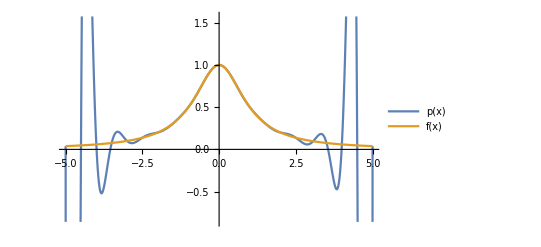

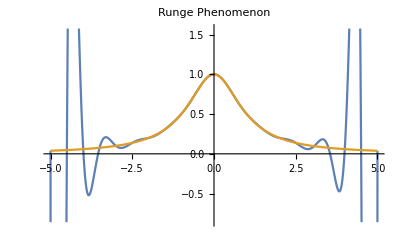

```mathematica
Plot[{p[x], f[x]}, {x, -5, 5}, PlotLegends->"Expressions"]
```

```mathematica
points
```

{{-5,1/26},{-4.5,0.0470588},{-4,1/17},{-3.5,0.0754717},{-3,1/10},{-2.5,0.137931},{-2,1/5},{-1.5,0.307692},{-1,1/2},{-0.5,0.8},{0,1},{0.5,0.8},{1,1/2},{1.5,0.307692},{2,1/5},{2.5,0.137931},{3,0.0754717},{3.5,0.0754717},{4,1/17},{4.5,0.0470588},{5,1/26}}

```mathematica
points2 = {{5.0,f[5]},{4.938441702975689,f[4.938441702975689]}, {  4.755282581475767,f[4.755282581475767]}, { 4.455032620941839,f[4.455032620941839]}, { 4.045084971874737,f[4.045084971874737]}, {  3.5355339059327378,f[  3.5355339059327378]}, {2.9389262614623664,f[2.9389262614623664]}, {2.269952498697734,f[2.269952498697734]}, {1.5450849718747373,f[1.5450849718747373]}, { 0.7821723252011547,f[0.7821723252011547]}, { 3.061616997868383e-16,f[ 3.061616997868383e-16]}, {-0.782172325201153, f[-0.782172325201153]} ,{-1.5450849718747368, f[-1.5450849718747368]},{-2.2699524986977337,f[-2.2699524986977337]} ,{-2.938926261462365, f[-2.938926261462365]},{-3.5355339059327373 , f[-3.5355339059327373]},{-4.045084971874736, f[-4.045084971874736]},{-4.455032620941839, f[-4.455032620941839]},{-4.755282581475767, f[-4.755282581475767]},{-4.938441702975688, f[-4.938441702975688]},{-5.0, f[-5]}}
```

{{5.,1/26},{4.93844,0.0393884},{4.75528,0.0423501},{4.45503,0.0479678},{4.04508,0.0575947},{3.53553,0.0740741},{2.93893,0.103764},{2.26995,0.162531},{1.54508,0.295221},{0.782172,0.620427},{-16+3.06162 e,1/(1+(-16+3.06162 e)^2)},{-0.782172,0.620427},{-1.54508,0.295221},{-2.26995,0.162531},{-2.93893,0.103764},{-3.53553,0.0740741},{-4.04508,0.0575947},{-4.45503,0.0479678},{-4.75528,0.0423501},{-4.93844,0.0393884},{-5.,1/26}}

```mathematica
g[x_]:=InterpolatingPolynomial[points2, x]
```

```mathematica
Function[x,InterpolatingPolynomial[points2,x]]
```

Function[x,InterpolatingPolynomial[points2,x]]

```mathematica
{{5.,1/26},{4.938441702975689,0.039388367265096015},{4.755282581475767,0.04235488950138765},{4.455032620941839,0.047968475118152346},{4.045084971874737,0.04807114529503665},{3.5355339059327378,0.07407538959812268},{2.9389262614623664,0.10382227951366321},{2.269952498697734,0.16264497156233992},{1.5450849718747373,0.2952443516064983},{0.7821723252011547,0.6217358865953743},{-16+3.061616997868383 e,1},{-0.782172325201153,0.6205306281507442},{-1.5450849718747368,0.2952443516064983},{-2.2699524986977337,0.1625369809624709},{-2.938926261462365,0.10382227951366321},{-3.5355339059327373,0.07407538959812268},{-4.045084971874736,0.05759696809559945},{-4.455032620941839,0.047968475118152346},{-4.755282581475767,0.04235488950138765},{-4.938441702975688,0.039395136528573065},{-5.,1/26}}
```

{{5.,1/26},{4.93844,0.0393884},{4.75528,0.0423549},{4.45503,0.0479685},{4.04508,0.0480711},{3.53553,0.0740754},{2.93893,0.103822},{2.26995,0.162645},{1.54508,0.295244},{0.782172,0.621736},{-16+3.06162 e,1},{-0.782172,0.620531},{-1.54508,0.295244},{-2.26995,0.162537},{-2.93893,0.103822},{-3.53553,0.0740754},{-4.04508,0.057597},{-4.45503,0.0479685},{-4.75528,0.0423549},{-4.93844,0.0393951},{-5.,1/26}}

```mathematica
points2
```

{{5.,1/26},{4.93844,0.0393884},{4.75528,0.0423549},{4.45503,0.0479685},{4.04508,0.0480711},{3.53553,0.0740754},{2.93893,0.103822},{2.26995,0.162645},{1.54508,0.295244},{0.782172,0.621736},{-16+3.06162 e,1},{-0.782172,0.620531},{-1.54508,0.295244},{-2.26995,0.162537},{-2.93893,0.103822},{-3.53553,0.0740754},{-4.04508,0.057597},{-4.45503,0.0479685},{-4.75528,0.0423549},{-4.93844,0.0393951},{-5.,1/26}}

```mathematica
g[x_]:=InterpolatingPolynomial[points2, x]
```

```mathematica
Function[x,InterpolatingPolynomial[points2,x]]
```

Function[x,InterpolatingPolynomial[points2,x]]

```mathematica
Function[x,InterpolatingPolynomial[points2,x]]
```

Function[x,InterpolatingPolynomial[points2,x]]

```mathematica
points2
```

{{5.,1/26},{4.93844,0.0393884},{4.75528,0.0423549},{4.45503,0.0479685},{4.04508,0.0480711},{3.53553,0.0740754},{2.93893,0.103822},{2.26995,0.162645},{1.54508,0.295244},{0.782172,0.621736},{-16+3.06162 e,1},{-0.782172,0.620531},{-1.54508,0.295244},{-2.26995,0.162537},{-2.93893,0.103822},{-3.53553,0.0740754},{-4.04508,0.057597},{-4.45503,0.0479685},{-4.75528,0.0423549},{-4.93844,0.0393951},{-5.,1/26}}

```mathematica
points2
```

{{5.,1/26},{4.93844,0.0393884},{4.75528,0.0423549},{4.45503,0.0479685},{4.04508,0.0480711},{3.53553,0.0740754},{2.93893,0.103822},{2.26995,0.162645},{1.54508,0.295244},{0.782172,0.621736},{-16+3.06162 e,1},{-0.782172,0.620531},{-1.54508,0.295244},{-2.26995,0.162537},{-2.93893,0.103822},{-3.53553,0.0740754},{-4.04508,0.057597},{-4.45503,0.0479685},{-4.75528,0.0423549},{-4.93844,0.0393951},{-5.,1/26}}

```mathematica
Plot[f[x], {x, -5,5}]
```

-Graphics-

```mathematica
g= Interpolation[points]
```

InterpolatingFunction[{{-5., 5.}}, <>]

```mathematica
Function[x,InterpolatingPolynomial[points,x]]
```

Function[x,InterpolatingPolynomial[points,x]]

```mathematica
Function[x,Interpolation[points]]
```

Function[x,Interpolation[points]]

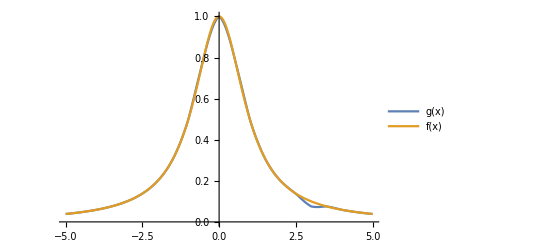

```mathematica
Plot[{g[x], f[x]}, {x, -5, 5}, PlotLegends->"Expressions"]
```

```mathematica
prob = (x^3 - 9x^2 + 26x - 24)/-6 + 8 *(x^3 - 8x^2 + 19x - 12)/2 + 27*(x^3 - 7x^2 + 14x - 8)/-2 + 64*(x^3 - 6x^2 + 11x - 6)/6
```

27/2 (8-14 x+7 x^2-x^3)+1/6 (24-26 x+9 x^2-x^3)+4 (-12+19 x-8 x^2+x^3)+32/3 (-6+11 x-6 x^2+x^3)

```mathematica
27/□ (8-12 x+7 x^2-x^3)+1/6 (24-20 x+9 x^2-x^3)+4 (-12+16 x-8 x^2+x^3)+32/3 (-6+6 x-6 x^2+x^3)
```

```mathematica
Simplify[prob]
```

x^3

```mathematica
InterpolatingPolynomial[{{1, 1}, {2, 8}, {3, 27}, {4, 64}},x]
```

1+(-1+x) (7+(-2+x) (3+x))

```mathematica
Expand[1+(-1+x) (7+(-2+x) (3+x))]
```

x^3

```mathematica
Plot[x^3, {x, 0, 5}]
```

```mathematica
3
Integrate[x^4 - 1/3x^2, {x, -1, 1}]
```

3

```mathematica
8/45
Integrate[x^2, {x, -1, 1}]
```

8/45

2/3

```mathematica
8/45 * 3/2
```

4/15

```mathematica
Integrate[x(x^3-3/5x)(x^2-1/3), {x, -1, 1}]
```

8/175

```mathematica
Integrate[(x^2-1/3)^2, {x ,-1, 1}]
```

8/45

```mathematica
8/175 * 45/8
```

9/35

```mathematica
Integrate[x(x^4- 6/7x^2- 3/35)(x^3-3/5x), {x, -1, 1}]
```

128/11025

```mathematica
Integrate[(x^3-3/5x)^2, {x, -1, 1}]
```

8/175

```mathematica
128/11025 * 175/8
```

16/63

```mathematica
Integrate[e^x (x- 1/2), {x, 0, 1}]
```

(2-2 e+Log[e]+e Log[e])/(2 Log[e]^2)

```mathematica
Integrate[(x - 1/2)^2, {x, 0, 1}]
```

1/12

```mathematica
Integrate[E^x (Sqrt[3](2x - 1)), {x, 0, 1}]/Integrate[(Sqrt[3](2x - 1))^2, {x, 0, 1}]
```

-√3 (-3+ⅇ)

```mathematica
N[Log[e]]
```

Log[e]

```mathematica
Log[10]
```

Log[10]

```mathematica
N[Log[10]]
```

2.30259

```mathematica
Log[E]
```

1

```mathematica
E
```

ⅇ

```mathematica
E^x - E^x + 1 - (-Sqrt[3](-3 + E))
```

1+√3 (-3+ⅇ)

```mathematica
E^x - E^x + 1 - (-Sqrt[3](-3 + E))/ Sqrt[Integrate[(E^x - E^x + 1 - (-Sqrt[3](-3 + E)))^2, {x, 0, 1}]]
```

1+(√3 (-3+ⅇ))/(1+√3 (-3+ⅇ))

```mathematica
(x - 1/2)/ Sqrt[Integrate[(x - 1/2)^2, {x, 0, 1}]]
```

2 √3 (-1/2+x)

```mathematica
3/ x - 2/x
```

1/x

```mathematica
8/x - 12/x
```

-4/x

```mathematica
9/8 * 16/5
```

18/5